```mathematica
<<FeynArts`
<<FormCalc`
_Hel=0;
$FAVerbose=0;
$FCVerbose=0;
```

FeynArts 3.9

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

last revised 2 Dec 14

FormCalc 8.4

by Thomas Hahn

last revised 23 Jan 15

## QCD 2->2 tree level parton processes

### qq’->qq’

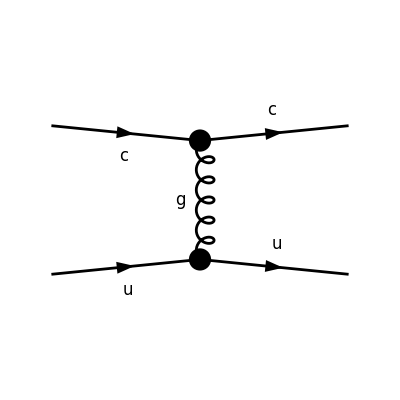

```mathematica
top1=CreateTopologies[0,2->2];
diags1=InsertFields[top1,{F[3,{2}],F[3,{1}]}->{F[3,{2}],F[3,{1}]},InsertionLevel->{Classes},Model->"SMQCD",ExcludeParticles->{S[1],S[2],V[1],V[2]}];
Paint[%,ColumnsXRows->{2,1},Numbering->None,SheetHeader->False];
```

```mathematica
ClearProcess[]
amp1=CalcFeynAmp[CreateFeynAmp[diags1],FermionChains->VA];
res1=(2^2/3^2 SquaredME[amp1]//.HelicityME[amp1]//.ColourME[amp1]//.Subexpr[]//.{Den[p2_,m2_]:>1/(p2-m2),MU2->0,MC2->0,MC->0,MU->0,T->-S-U,Alfas2->(gS^2/(4 π))^2}//Simplify)/.{S+U->T}
```

running FORM... running FORM...

(4 gS^4 (S^2+U^2))/(9 T^2)

### qOverBar[q']->qOverBar[q']

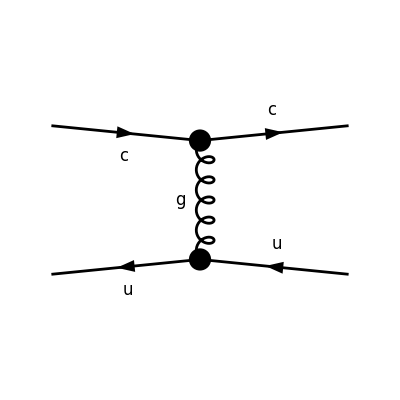

```mathematica
top2=CreateTopologies[0,2->2];
diags2=InsertFields[top2,{F[3,{2}],-F[3,{1}]}->{F[3,{2}],-F[3,{1}]},InsertionLevel->{Classes},Model->"SMQCD",ExcludeParticles->{S[1],S[2],V[1],V[2]}];
Paint[%,ColumnsXRows->{2,1},Numbering->None,SheetHeader->False];
```

```mathematica
ClearProcess[];
amp2=CalcFeynAmp[CreateFeynAmp[diags2],FermionChains->VA];
res2=(2^2/3^2 SquaredME[amp2]//.HelicityME[amp2]//.ColourME[amp2]//.Subexpr[]//.{Den[p2_,m2_]:>1/(p2-m2),MU2->0,MC2->0,MC->0,MU->0,T->-S-U,Alfas2->(gS^2/(4 π))^2}//Simplify)/.{S+U->T}
```

running FORM... running FORM...

(4 gS^4 (S^2+U^2))/(9 T^2)

### qq->qq

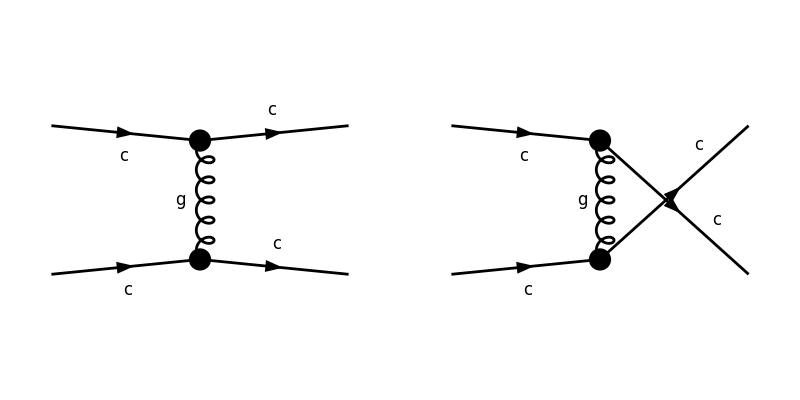

```mathematica
top3=CreateTopologies[0,2->2];
diags3=InsertFields[top3,{F[3,{2}],F[3,{2}]}->{F[3,{2}],F[3,{2}]},InsertionLevel->{Classes},Model->"SMQCD",ExcludeParticles->{S[1],S[2],V[1],V[2]}];
Paint[%,ColumnsXRows->{2,1},Numbering->None,SheetHeader->False];
```

```mathematica
ClearProcess[];
amp3=CalcFeynAmp[CreateFeynAmp[diags3],FermionChains->VA];
res3=(2^2/3^2 SquaredME[amp3]//.HelicityME[amp3]//.ColourME[amp3]//.Subexpr[]//.{Den[p2_,m2_]:>1/(p2-m2),MU2->0,MC2->0,MC->0,MU->0,T->-S-U,Alfas2->(gS^2/(4 π))^2}//Simplify)/.{S+U->T}
```

running FORM... running FORM...

(8 gS^4 (3 S^4+10 S^3 U+13 S^2 U^2+6 S U^3+3 U^4))/(27 T^2 U^2)

```mathematica
(res3+(8 gS^4 S^2)/(27 T U)-4/9 gS^4((S^2+T^2)/U^2)-4/9 gS^4((S^2+U^2)/T^2))//Simplify[#//.U->-S-T]&
```

0

### qq̄->q’OverBar[q']

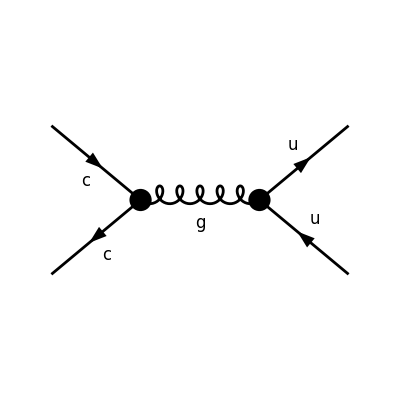

```mathematica
top4=CreateTopologies[0,2->2];
diags4=InsertFields[top4,{F[3,{2}],-F[3,{2}]}->{F[3,{1}],-F[3,{1}]},InsertionLevel->{Classes},Model->"SMQCD",ExcludeParticles->{S[1],S[2],V[1],V[2]}];
Paint[%,ColumnsXRows->{2,1},Numbering->None,SheetHeader->False];
```

```mathematica
ClearProcess[];
amp4=CalcFeynAmp[CreateFeynAmp[diags4],FermionChains->VA];
res4=(2^2/3^2 SquaredME[amp4]//.HelicityME[amp4]//.ColourME[amp4]//.Subexpr[]//.{Den[p2_,m2_]:>1/(p2-m2),MU2->0,MC2->0,MC->0,MU->0,T->-S-U,Alfas2->(gS^2/(4 π))^2}//Simplify)/.{S+U->T}
```

running FORM... running FORM...

(4 gS^4 (S^2+2 S U+2 U^2))/(9 S^2)

### qq̄->qq̄

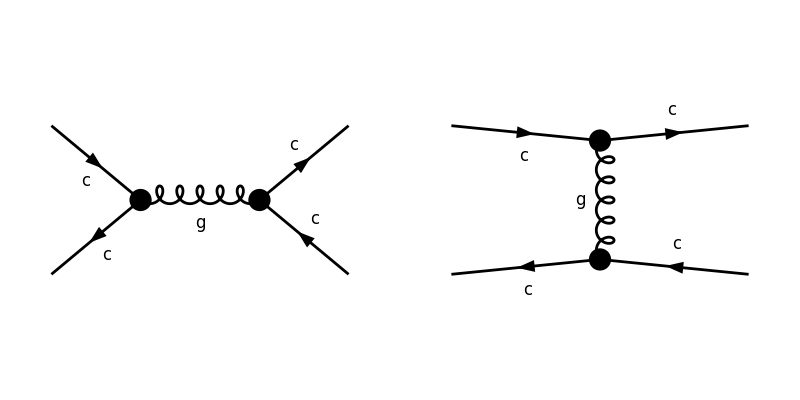

```mathematica
top5=CreateTopologies[0,2->2];
diags5=InsertFields[top5,{F[3,{2}],-F[3,{2}]}->{F[3,{2}],-F[3,{2}]},InsertionLevel->{Classes},Model->"SMQCD",ExcludeParticles->{S[1],S[2],V[1],V[2]}];
Paint[%,ColumnsXRows->{2,1},Numbering->None,SheetHeader->False];
```

```mathematica
ClearProcess[];
amp5=CalcFeynAmp[CreateFeynAmp[diags5],FermionChains->VA];
res5=(2^2/3^2 SquaredME[amp5]//.HelicityME[amp5]//.ColourME[amp5]//.Subexpr[]//.{Den[p2_,m2_]:>1/(p2-m2),MU2->0,MC2->0,MC->0,MU->0,T->-S-U,Alfas2->(gS^2/(4 π))^2}//Simplify)/.{S+U->T}
```

running FORM... running FORM...

(8 gS^4 (3 S^4+6 S^3 U+13 S^2 U^2+10 S U^3+3 U^4))/(27 S^2 T^2)

```mathematica
(res5+(8 gS^4 U^2)/(27 S T)-4/9 gS^4((S^2+U^2)/T^2)-4/9 gS^4((T^2+U^2)/S^2))//Simplify[#//.U->-S-T]&
```

0

### qq̄->gg

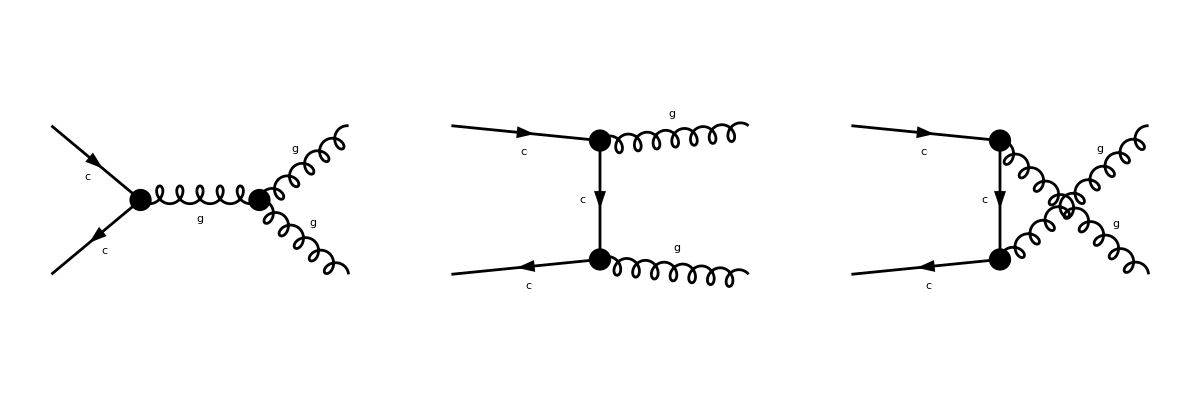

```mathematica
top6=CreateTopologies[0,2->2];
diags6=InsertFields[top6,{F[3,{2}],-F[3,{2}]}->{V[5],V[5]},InsertionLevel->{Classes},Model->"SMQCD",ExcludeParticles->{S[1],S[2],V[1],V[2]}];
Paint[%,ColumnsXRows->{3,1},Numbering->None,SheetHeader->False];
```

```mathematica
ClearProcess[];
amp6=CalcFeynAmp[CreateFeynAmp[diags6],FermionChains->VA];
res6=(1/3^2)SquaredME[amp6]//.HelicityME[amp6]//.ColourME[amp6]//.Subexpr[];
res61= PolarizationSum[res6,GaugeTerms->False]//.Subexpr[]//.{Den[p2_,m2_]:>1/(p2-m2),MU2->0,MC2->0,MC->0,MU->0,Alfas2->(gS^2/(4π))^2}//Simplify[#]&//Expand
```

running FORM... running FORM... running FORM...

-(64 gS^4)/27+(4 gS^4 S)/(27 T)-(16 gS^4 T)/(3 S)-(16 gS^4 T^2)/(3 S^2)+(4 gS^4 S)/(27 U)+(4 gS^4 T)/(3 U)-(16 gS^4 U)/(3 S)+(4 gS^4 U)/(3 T)-(16 gS^4 T U)/(3 S^2)-(16 gS^4 U^2)/(3 S^2)

```mathematica
(res61-((32 gS^4 )/27 )((T^2+U^2)/(T U))+8/3 gS^4((T^2+U^2)/S^2))//Simplify[#//.U->-S-T]&
```

0

### gg->qq̄

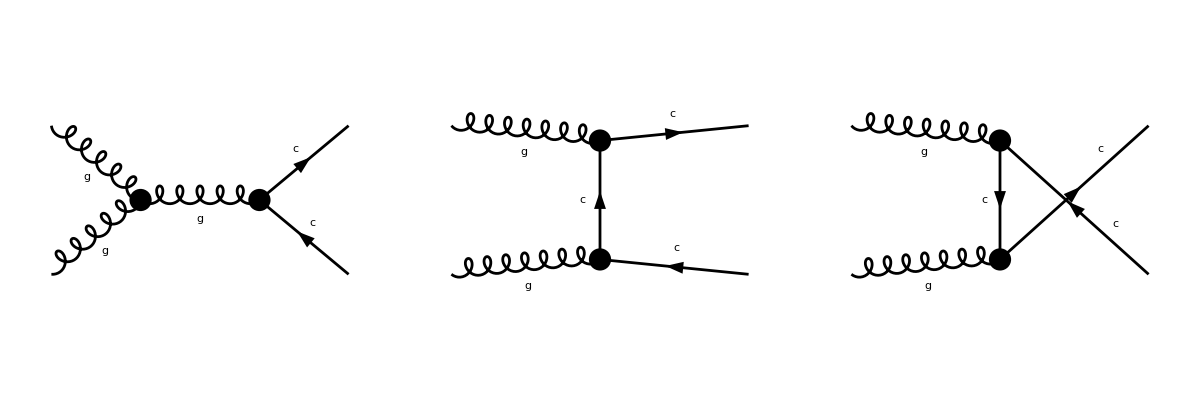

```mathematica
top7=CreateTopologies[0,2->2];
diags7=InsertFields[top7,{V[5],V[5]}->{F[3,{2}],-F[3,{2}]},InsertionLevel->{Classes},Model->"SMQCD",ExcludeParticles->{S[1],S[2],V[1],V[2]}];
Paint[%,ColumnsXRows->{3,1},Numbering->None,SheetHeader->False];
```

```mathematica
ClearProcess[];
amp7=CalcFeynAmp[CreateFeynAmp[diags7],FermionChains->VA];
res7=(2^2/(2^2 8^2))SquaredME[amp7]//.HelicityME[amp7]//.ColourME[amp7]//.Subexpr[];
res71= PolarizationSum[res7,GaugeTerms->False]//.Subexpr[]//.{Den[p2_,m2_]:>1/(p2-m2),MU2->0,MC2->0,MC->0,MU->0,Alfas2->(gS^2/(4π))^2}//Simplify[#]&//Expand
```

running FORM... running FORM... running FORM...

(5 gS^4)/24+(5 gS^4 S)/(96 T)+(19 gS^4 S)/(96 U)+(gS^4 S^2)/(48 T U)-(gS^4 T)/(32 U)-(3 gS^4 T^2)/(8 S U)-(17 gS^4 U)/(96 T)+(3 gS^4 T U)/(4 S^2)-(3 gS^4 U^2)/(8 S T)

```mathematica
(res71-((1 gS^4 )/6 )((T^2+U^2)/(T U))+3/8 gS^4((T^2+U^2)/S^2))//Simplify[#//.U->-S-T]&
```

0

### gq->gq

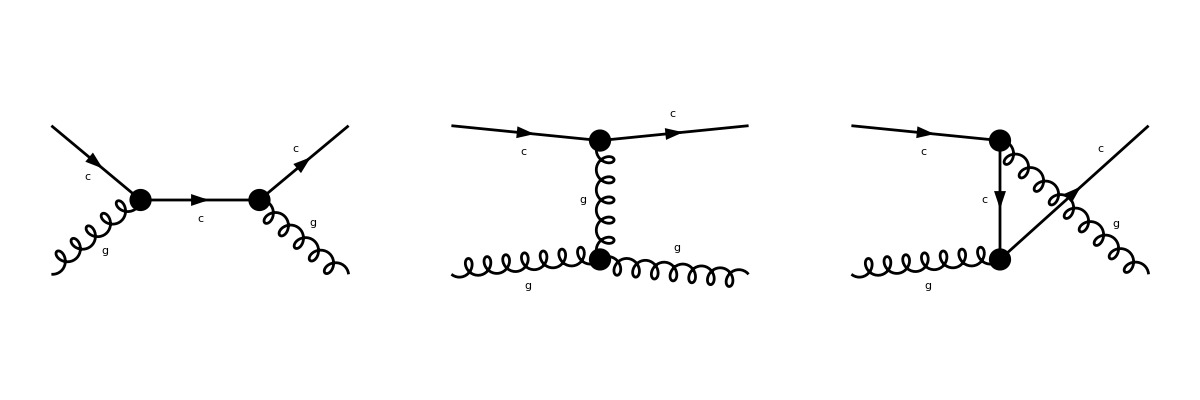

```mathematica
top8=CreateTopologies[0,2->2];
diags8=InsertFields[top8,{F[3,{2}],V[5]}->{F[3,{2}],V[5]},InsertionLevel->{Classes},Model->"SMQCD",ExcludeParticles->{S[1],S[2],V[1],V[2]}];
Paint[%,ColumnsXRows->{3,1},Numbering->None,SheetHeader->False];
```

```mathematica
ClearProcess[];
amp8=CalcFeynAmp[CreateFeynAmp[diags8],FermionChains->VA];
res8=(2/(2*3*8))SquaredME[amp8]//.HelicityME[amp8]//.ColourME[amp8]//.Subexpr[];
res81= PolarizationSum[res8,GaugeTerms->False]//.Subexpr[]//.{Den[p2_,m2_]:>1/(p2-m2),MU2->0,MC2->0,MC->0,MU->0,Alfas2->(gS^2/(4π))^2}//Simplify[#]&//Expand
```

running FORM... running FORM... running FORM...

(3 gS^4)/4+(gS^4 S^2)/T^2+(19 gS^4 S)/(8 T)-(gS^4 T)/(8 S)+(17 gS^4 S)/(72 U)+(9 gS^4 S^2)/(8 T U)-(37 gS^4 T)/(72 U)-(5 gS^4 T^2)/(72 S U)+(5 gS^4 U)/(8 S)+(19 gS^4 U)/(8 T)+(gS^4 U^2)/T^2+(9 gS^4 U^2)/(8 S T)

```mathematica
(res81+((4 gS^4 )/9 )((S^2+U^2)/(S U))-gS^4((S^2+U^2)/T^2))//Simplify[#//.U->-S-T]&
```

0

### gg->gg

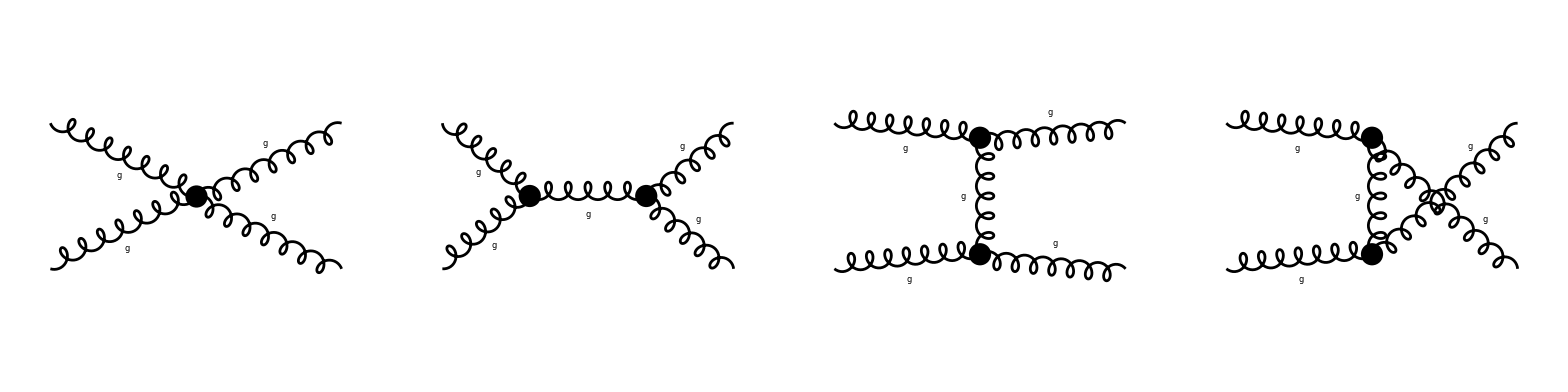

```mathematica
top9=CreateTopologies[0,2->2];
diags9=InsertFields[top9,{V[5],V[5]}->{V[5],V[5]},InsertionLevel->{Classes},Model->"SMQCD",ExcludeParticles->{S[1],S[2],V[1],V[2]}];
Paint[%,ColumnsXRows->{4,1},Numbering->None,SheetHeader->False];
```

```mathematica
ClearProcess[];
amp9=CalcFeynAmp[CreateFeynAmp[diags9],FermionChains->VA];
res9=(1/(2^2*8^2))SquaredME[amp9]//.ColourME[amp9]//.Subexpr[];
res91= PolarizationSum[res9,GaugeTerms->False]//.Subexpr[]//.{Den[p2_,m2_]:>1/(p2-m2),MU2->0,MC2->0,MC->0,MU->0,Alfas2->(gS^2/(4π))^2}//Simplify[#]&//Expand
```

running FORM... running FORM...

(63 gS^4)/8-(9 gS^4 S^2)/(4 T^2)-(63 gS^4 T)/(8 S)+(9 gS^4 S^2)/(2 U^2)+(27 gS^4 S)/(4 U)+(9 gS^4 T)/(2 U)+(9 gS^4 T^2)/(4 S U)-(63 gS^4 U)/(8 S)-(27 gS^4 S U)/(4 T^2)+(9 gS^4 U)/(2 T)-(9 gS^4 T U)/(2 S^2)+(9 gS^4 U^2)/(4 S T)

```mathematica
(res91-((9 gS^4 )/2 )(3-(T U)/S^2-(S U)/T^2-(S T)/U^2))//Simplify[#//.U->-S-T]&
```

0